```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
σSB=5.67*10^(-5); 
a=4*σSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,5}];
```

```mathematica
Model0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\RG_3_1727\\Model1727.dat","Table"];

Model=Drop[Model0,1];
```

```mathematica
RadiusMass=Model[[All,{6,5}]];
RadiusLogTemp=Model[[All,{6,3}]];
RadiusTemp=Table[{RadiusLogTemp[[i,1]],10^RadiusLogTemp[[i,2]]},{i,1,Dimensions[RadiusLogTemp][[1]]}];
RadiusLogDens=Model[[All,{6,4}]];
RadiusDens=Table[{RadiusLogDens[[i,1]],10^RadiusLogDens[[i,2]]},{i,1,Dimensions[RadiusLogDens][[1]]}];
RadiusLogPress=Model[[All,{6,2}]];
RadiusPress=Table[{RadiusLogPress[[i,1]],10^RadiusLogPress[[i,2]]},{i,1,Dimensions[RadiusLogPress][[1]]}];
RadiusLumin=Model[[All,{6,7}]];
RadiusOpacity=Model[[All,{6,9}]];
RadiusGrav=Table[{RadiusMass[[i,1]], (G*RadiusMass[[i,2]])/RadiusMass[[i,1]]^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];
OpacityN=Interpolation[RadiusOpacity];
```

```mathematica
Rtot=Model[[1,6]]/Model[[1,16]];

RDown=1*10^-2*Rtot;
RUp=80*10^-2*Rtot;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
RadiusOpacityReduced=Select[RadiusOpacity,RDown<#[[1]]<RUp&];
```

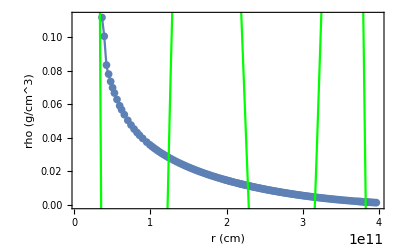

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None]
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

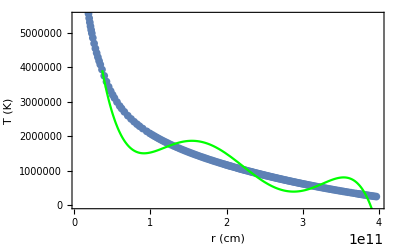

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None]
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None]
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
SoundSpeed[R_,z_]=√(γ P[R,z] / ρ[R,z]);
```

-Graphics-

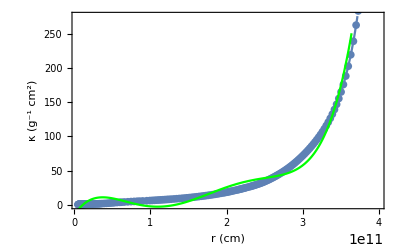

```mathematica
κFit0=Fit[RadiusOpacityReduced,Polinomi,q];
κFit[x_]=κFit0/.{q->x};
Show[Plot[OpacityN[r],{r,RDown,RUp}],ListPlot[RadiusOpacityReduced],Plot[κFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","κ (g^-1 cm^2)","Opacity"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None]
κ[R_,z_]=κFit[(R^2+z^2)^0.5];
```

```mathematica
σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
Mu=0.62;
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*κ[R,z]*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(κ[R,z]*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
Pr[R_,z_]=ν[R,z]/χ[R,z];
```

```mathematica
Mu=0.62;
χN[R_,z_]=(16*TN[√(R^2+z^2)]^3*σSB*(γ-1)*Mu*mP)/(3*OpacityN[√(R^2+z^2)]*RhoN[√(R^2+z^2)]^2*kB);   (*this is what Goldreich and Schubert call χ*)
Λ=10^4;    νdynN[R_,z_]=2.2*10^-15*(TN[√(R^2+z^2)]^(5/2))/(RhoN[√(R^2+z^2)]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νradN[R_,z_]=16/15*(σSB*TN[√(R^2+z^2)]^4)/(OpacityN[√(R^2+z^2)]*RhoN[√(R^2+z^2)]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
νN[R_,z_]=νradN[R,z]+νdynN[R,z];
PrN[R_,z_]=νN[R,z]/χN[R,z];
```

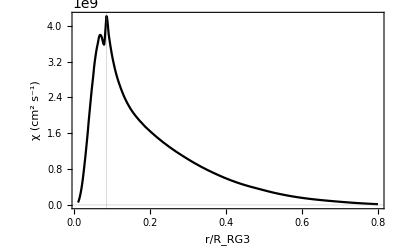

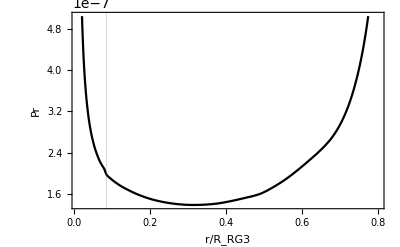

```mathematica
PlotχN=Plot[χN[r*Rtot*Sin[π/4],r*Rtot*Cos[π/4]],{r,RDown/Rtot,RUp/Rtot},Frame->True,FrameLabel->{"r/R_RG3","χ (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black,Axes->False,GridLines->{{0.085},{10}}]
Show[LogPlot[νN[r*Rtot*Sin[π/4],r*Rtot*Cos[π/4]],{r,RDown/Rtot,RUp/Rtot},PlotStyle->Directive[Black],PlotRange->{{RDown/Rtot,RUp/Rtot},{0.1,1000}}],LogPlot[νdynN[r*Rtot*Sin[π/4],r*Rtot*Cos[π/4]],{r,RDown/Rtot,RUp/Rtot},PlotStyle->Directive[Black,Dashed],PlotRange->{{RDown/Rtot,RUp/Rtot},{0.1,1000}}],LogPlot[νradN[r*Rtot*Sin[π/4],r*Rtot*Cos[π/4]],{r,RDown/Rtot,RUp/Rtot},PlotStyle->Directive[Black,Dotted],PlotRange->{{RDown/Rtot,RUp/Rtot},{0.1,1000}}],Frame->True,FrameLabel->{"r/R_RG3","ν (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},GridLines->{{0.085},{10}}];
PlotPrN=Plot[PrN[r*Rtot*Sin[π/4],r*Rtot*Cos[π/4]],{r,RDown/Rtot,RUp/Rtot},Frame->True,FrameLabel->{"r/R_RG3","Pr"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black,Axes->False,GridLines->{{0.085},{10}}]
```

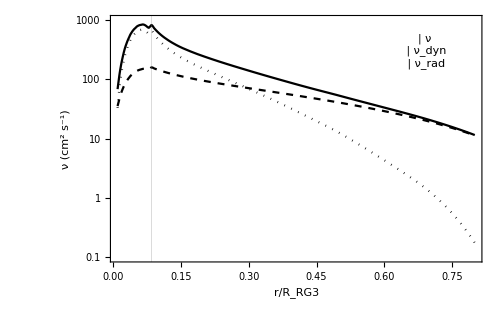

-Graphics-

```mathematica
CaptionGeneral[{{"ν", Black, Automatic},{"ν_dyn",Black,Dashed},{"ν_rad",Black,Dotted}}]
```

CaptionGeneral[{{ν,-Graphics-,Automatic},{ν_dyn,-Graphics-,Dashing[{Small,Small}]},{ν_rad,-Graphics-,Dashing[{0,Small}]}}]

```mathematica
PlotνN=-Graphics-;
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\RG_3_1727\\picRG3HeatDiffusivity.png",PlotχN,ImageResolution->150]
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\RG_3_1727\\picRG3Viscosity.png",PlotνN,ImageResolution->150]
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\RG_3_1727\\picRG3Prandtl.png",PlotPrN,ImageResolution->150]*)
```